Post Lab: Fitting Data to an Assumed Distribution

1.

```mathematica
y[x_]:=RandomVariate[PoissonDistribution[x],1000];
```

2.

```mathematica
Data = y[5];
DataCounts=BinCounts[Data,{0,19,1}];
bins = Table[i,{i,0,Length[DataCounts]-1}];
TwoDList=Multicolumn[Join[bins,DataCounts],2]//First
```

{{0,9},{1,42},{2,86},{3,144},{4,174},{5,165},{6,155},{7,95},{8,67},{9,33},{10,17},{11,9},{12,3},{13,1},{14,0},{15,0},{16,0},{17,0},{18,0}}

3.

```mathematica
TotalPoints=Sum[DataCounts[[i]],{i,1,Length[DataCounts]}]
NormedDataCounts = DataCounts/TotalPoints;
NormedTwoDList=Multicolumn[Join[bins,NormedDataCounts],2]//First;
```

1000

4.

```mathematica
DataMean = Sum[(bins[[i]])*DataCounts[[i]],{i,1,Length[DataCounts]}]/TotalPoints//N
```

4.913

5.

```mathematica
g = 1/(√(2 σ^2 π))ⅇ^(-(x-DataMean)^2/(2 σ^2));
```

```mathematica
f = FindFit[NormedDataCounts,g,{σ},x];
sig = f[[1,2]]
(*mn=f[[2,2]]*)
```

2.37883

6.

```mathematica
myGauss[x_]:=1/(√(2*(sig)^2*π))ⅇ^(-(x-DataMean)^2/(2 (sig)^2))
```

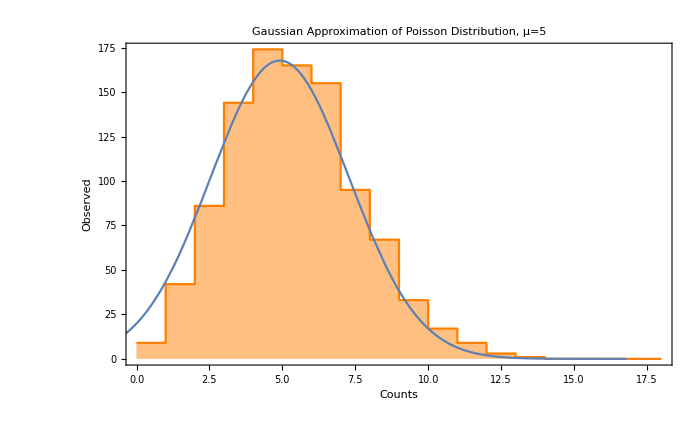

```mathematica
(*Abscissa labels correspond to the value of the bin. The plotted Gaussian curve values correspond to the center of each bin*)
histTwo=Histogram[Data];
histThree=ListPlot[TwoDList,Joined->True,InterpolationOrder->0,PlotRange->Automatic,Filling->Axis,FillingStyle->{Lighter[Orange,0.5]},PlotStyle->{Orange},AxesOrigin->{0,0},FrameLabel->{Style["Counts",Black,24],Style["Observed",Black,24]},Frame->True,PlotLabel->Style["Gaussian Approximation of Poisson Distribution, μ=5",Black,30],FrameTicksStyle->Directive[Black,18]];
curve=Plot[Length[Data]*myGauss[x],{x,DataMean-5*sig,DataMean+5*sig},AxesOrigin->{0,0}];
Show[histThree,curve]
```